```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=√(m^2+p^2);Nx=50;
```

```mathematica
α=1;m =5/2;λ=π/2;
```

```mathematica
ϕ[n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[n_]:=ω[p]ϕ[n][p]-λ Integrate[(ϕ[n][k]-ϕ[n][p])/(p-k)^2,{k,-∞,∞},PrincipalValue->True,GenerateConditions->False]
```

```mathematica
Table[Integrate[ϕ[i][p]H[n],{p,-∞,∞},GenerateConditions->False],{i,0,Nx},{n,0,Nx}]//AbsoluteTiming
```

{{HypergeometricU[-1/2,0,25/4],0,(-4 π^2+25 ⅇ^(25/8) (-BesselK[0,25/8]+BesselK[1,25/8]))/(8 √(2 π)),0,(24 π^2+25 ⅇ^(25/8) (31 BesselK[0,25/8]-27 BesselK[1,25/8]))/(32 √(6 π)),0,-1/384 √(5/π) (48 π^2+5 ⅇ^(25/8) (1135 BesselK[0,25/8]-987 BesselK[1,25/8])),0,1/512 √(5/(14 π)) (224 π^2+25 ⅇ^(25/8) (3281 BesselK[0,25/8]-2853 BesselK[1,25/8])),0,(-12096 π^2+25 ⅇ^(25/8) (-489899 BesselK[0,25/8]+425991 BesselK[1,25/8]))/(18432 √(7 π))},{0,(25 ⅇ^(25/8) BesselK[1,25/8])/(4 √π),-(ⅈ π^2)/4,(-π^2-75/4 ⅇ^(25/8) BesselK[1,25/8]+3 √π HypergeometricU[-1/2,-2,25/4])/(√(6 π)),1/8 ⅈ √3 π^2,(-32 π^2+75 ⅇ^(25/8) (-275 BesselK[0,25/8]+239 BesselK[1,25/8]))/(64 √(30 π)),-1/8 ⅈ √(5/2) π^2,(-3 π^2+25/64 ⅇ^(25/8) (33325 BesselK[0,25/8]-28977 BesselK[1,25/8]))/(12 √(35 π)),1/32 ⅈ √35 π^2,-(√(5/(14 π)) (384 π^2+175 ⅇ^(25/8) (44675 BesselK[0,25/8]-38847 BesselK[1,25/8])))/9216,-3/32 ⅈ √(7/2) π^2},{(25 ⅇ^(25/8) BesselK[1,25/8])/(4 √(2 π))-HypergeometricU[-1/2,0,25/4]/(√2),0,(8 π^2+75 ⅇ^(25/8) (9 BesselK[0,25/8]-5 BesselK[1,25/8]))/(32 √π),-1/2 ⅈ √(3/2) π^2,-1/128 √(3/π) (16 π^2+25 ⅇ^(25/8) (229 BesselK[0,25/8]-201 BesselK[1,25/8])),0,1/256 √(5/(2 π)) (32 π^2+15 ⅇ^(25/8) (2855 BesselK[0,25/8]-2483 BesselK[1,25/8])),0,-(√(35/π) (64 π^2+5 ⅇ^(25/8) (53755 BesselK[0,25/8]-46743 BesselK[1,25/8])))/2048,0,(8064 π^2+25 ⅇ^(25/8) (3783641 BesselK[0,25/8]-3290061 BesselK[1,25/8]))/(12288 √(14 π))},{0,(25 ⅇ^(25/8) (25 BesselK[0,25/8]-21 BesselK[1,25/8]))/(16 √(6 π)),0,(9 π^2-25/32 ⅇ^(25/8) (625 BesselK[0,25/8]-597 BesselK[1,25/8]))/(6 √π),0,1/256 √(5/π) (-64 π^2+25 ⅇ^(25/8) (1475 BesselK[0,25/8]-1279 BesselK[1,25/8])),0,(-84 π^2-25/32 ⅇ^(25/8) (902425 BesselK[0,25/8]-784653 BesselK[1,25/8]))/(48 √(210 π)),0,(-2592 π^2+25/8 ⅇ^(25/8) (42689725 BesselK[0,25/8]-37120641 BesselK[1,25/8]))/(4608 √(105 π)),0},{(25 ⅇ^(25/8) (31 BesselK[0,25/8]-27 BesselK[1,25/8]))/(32 √(6 π)),0,(16 π^2+75 ⅇ^(25/8) (-229 BesselK[0,25/8]+201 BesselK[1,25/8]))/(128 √(3 π)),(ⅈ π^2)/(√2),(-96 π^2+25 ⅇ^(25/8) (21247 BesselK[0,25/8]-18027 BesselK[1,25/8]))/(1536 √π),-1/2 ⅈ √(5/2) π^2,(√(5/(6 π)) (192 π^2+25 ⅇ^(25/8) (-158219 BesselK[0,25/8]+137703 BesselK[1,25/8])))/3072,0,(√(5/(21 π)) (-896 π^2+5 ⅇ^(25/8) (11674685 BesselK[0,25/8]-10151937 BesselK[1,25/8])))/8192,0,(48384 π^2+25 ⅇ^(25/8) (-354266963 BesselK[0,25/8]+308052687 BesselK[1,25/8]))/(147456 √(42 π))},{0,5/64 ⅇ^(25/8) √(15/(2 π)) (-275 BesselK[0,25/8]+239 BesselK[1,25/8]),0,1/256 √(5/π) (-64 π^2+25 ⅇ^(25/8) (1475 BesselK[0,25/8]-1279 BesselK[1,25/8])),0,(5 (384 π^2+25 ⅇ^(25/8) (-10075 BesselK[0,25/8]+8823 BesselK[1,25/8])))/(1024 √π),0,(5 (-1792 π^2+225 ⅇ^(25/8) (46175 BesselK[0,25/8]-40139 BesselK[1,25/8])))/(2048 √(42 π)),0,-(32256 π^2+25 ⅇ^(25/8) (98827975 BesselK[0,25/8]-85934931 BesselK[1,25/8]))/(49152 √(21 π)),0},{5/384 ⅇ^(25/8) √(5/π) (-1135 BesselK[0,25/8]+987 BesselK[1,25/8]),0,(32 π^2+75 ⅇ^(25/8) (2855 BesselK[0,25/8]-2483 BesselK[1,25/8]))/(256 √(10 π)),0,(-9 π^2-125/64 ⅇ^(25/8) (158219 BesselK[0,25/8]-137703 BesselK[1,25/8]))/(48 √(30 π)),1/2 ⅈ √3 π^2,(1152 π^2+125 ⅇ^(25/8) (1200463 BesselK[0,25/8]-1041531 BesselK[1,25/8]))/(36864 √π),-1/2 ⅈ √(7/2) π^2,-(5376 π^2+125 ⅇ^(25/8) (17786269 BesselK[0,25/8]-15467745 BesselK[1,25/8]))/(49152 √(14 π)),0,(290304 π^2+25 ⅇ^(25/8) (13551477155 BesselK[0,25/8]-11783705439 BesselK[1,25/8]))/(1769472 √(35 π))},{0,5/768 ⅇ^(25/8) √(5/(7 π)) (33325 BesselK[0,25/8]-28977 BesselK[1,25/8]),0,(-84 π^2-25/32 ⅇ^(25/8) (902425 BesselK[0,25/8]-784653 BesselK[1,25/8]))/(48 √(210 π)),0,(5 (-1792 π^2+225 ⅇ^(25/8) (46175 BesselK[0,25/8]-40139 BesselK[1,25/8])))/(2048 √(42 π)),0,(5 (225792 π^2+25 ⅇ^(25/8) (-51513025 BesselK[0,25/8]+44826837 BesselK[1,25/8])))/(516096 √π),0,(5 (-1354752 π^2+25 ⅇ^(25/8) (2461398325 BesselK[0,25/8]-2140214361 BesselK[1,25/8])))/(6193152 √(2 π)),0},{25/512 ⅇ^(25/8) √(5/(14 π)) (3281 BesselK[0,25/8]-2853 BesselK[1,25/8]),0,(√(5/(7 π)) (64 π^2+35 ⅇ^(25/8) (-53755 BesselK[0,25/8]+46743 BesselK[1,25/8])))/2048,0,(√(5/(21 π)) (-384 π^2+5 ⅇ^(25/8) (11674685 BesselK[0,25/8]-10151937 BesselK[1,25/8])))/8192,0,(5 (768 π^2+25 ⅇ^(25/8) (-17786269 BesselK[0,25/8]+15467745 BesselK[1,25/8])))/(49152 √(14 π)),ⅈ π^2,(5 (-1536 π^2+25 ⅇ^(25/8) (113533963 BesselK[0,25/8]-98696679 BesselK[1,25/8])))/(393216 √π),-(3 ⅈ π^2)/(2 √2),(√(5/(2 π)) (193536 π^2+25 ⅇ^(25/8) (-40496986613 BesselK[0,25/8]+35214669849 BesselK[1,25/8])))/16515072},{0,-(25 ⅇ^(25/8) √(35/(2 π)) (44675 BesselK[0,25/8]-38847 BesselK[1,25/8]))/9216,0,(-81 π^2+25/256 ⅇ^(25/8) (42689725 BesselK[0,25/8]-37120641 BesselK[1,25/8]))/(144 √(105 π)),0,-(32256 π^2+25 ⅇ^(25/8) (98827975 BesselK[0,25/8]-85934931 BesselK[1,25/8]))/(49152 √(21 π)),0,(5 (-1354752 π^2+25 ⅇ^(25/8) (2461398325 BesselK[0,25/8]-2140214361 BesselK[1,25/8])))/(6193152 √(2 π)),0,(5 (73156608 π^2+25 ⅇ^(25/8) (-117957495025 BesselK[0,25/8]+102580094661 BesselK[1,25/8])))/(148635648 √π),0},{-(25 ⅇ^(25/8) (489899 BesselK[0,25/8]-425991 BesselK[1,25/8]))/(18432 √(7 π)),0,(896 π^2+25 ⅇ^(25/8) (3783641 BesselK[0,25/8]-3290061 BesselK[1,25/8]))/(12288 √(14 π)),0,-(16128 π^2+25 ⅇ^(25/8) (354266963 BesselK[0,25/8]-308052687 BesselK[1,25/8]))/(147456 √(42 π)),0,(√(5/(7 π)) (32256 π^2+5 ⅇ^(25/8) (13551477155 BesselK[0,25/8]-11783705439 BesselK[1,25/8])))/1769472,0,-(√(5/(2 π)) (150528 π^2+25 ⅇ^(25/8) (40496986613 BesselK[0,25/8]-35214669849 BesselK[1,25/8])))/16515072,1/2 ⅈ √5 π^2,(8128512 π^2+25 ⅇ^(25/8) (6208730570527 BesselK[0,25/8]-5398577836683 BesselK[1,25/8]))/(594542592 √π)}}

```mathematica
N@%17
```

{{2.59491,0.,-1.84067,0.,1.69871,0.,-1.55558,0.,1.45572,0.,-1.38113},{0.,2.77598,0.-2.4674 ⅈ,-2.06397,0.+2.13683 ⅈ,-0.520269,0.-1.95065 ⅈ,-0.233603,0.+1.82467 ⅈ,-0.139004,0.-1.73103 ⅈ},{0.128033,0.,4.33386,0.-6.04387 ⅈ,-0.924086,0.,1.08245,0.,-1.02669,0.,0.97603},{0.,0.209292,0.,11.4484,0.,-2.76521,0.,-0.696936,0.,-0.301676,0.},{-0.00623356,0.,0.683352,0.+6.97886 ⅈ,2.89273,0.-7.80261 ⅈ,0.726656,0.,-0.328233,0.,0.287265},{0.,-0.0119524,0.,-2.76521,0.,13.8185,0.,-3.29254,0.,-0.835103,0.},{0.000810879,0.,0.202016,0.,0.21834,0.+8.54733 ⅈ,3.68244,0.-9.23217 ⅈ,0.358104,0.,0.110069},{0.,0.00170186,0.,-0.696936,0.,-3.29254,0.,15.8141,0.,-3.73403,0.},{-0.000156811,0.,0.149839,0.,-0.158416,0.,0.637141,0.+9.8696 ⅈ,3.6446,0.-10.4683 ⅈ,0.724932},{0.,-0.000349451,0.,-0.301676,0.,-0.835103,0.,-3.73403,0.,17.5723,0.},{0.0000382577,0.,0.107915,0.,-0.0886397,0.,0.0414389,0.,0.541509,0.+11.0346 ⅈ,4.05684}}

```mathematica
Sort@Eigenvalues[%17]
```

{2.52586-0.195091 ⅈ,2.52586+0.195091 ⅈ,2.96961+1.46243×10^-16 ⅈ,3.26081-2.90869×10^-16 ⅈ,4.06634-0.129137 ⅈ,4.06634+0.129137 ⅈ,4.70528-5.3209×10^-16 ⅈ,8.12277-2.64653×10^-16 ⅈ,12.7752-1.40143×10^-15 ⅈ,16.7421+7.74554×10^-16 ⅈ,20.8745+1.47442×10^-15 ⅈ}

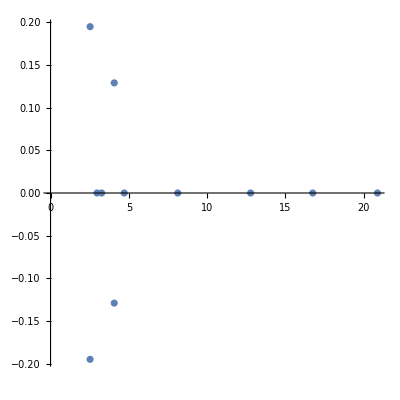

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%20,AspectRatio->1]
```

```mathematica
Eigenvalues[%12]
```

{15.6101+4.91631×10^-16 ⅈ,9.50457+8.96195×10^-16 ⅈ,4.11007-1.16647×10^-15 ⅈ,3.50735-5.6126×10^-16 ⅈ,2.56616+0.204308 ⅈ,2.56616-0.204308 ⅈ}

```mathematica
Integrate[ϕ[i][p]H[n],{p,-∞,∞}]
```